------------------------------------------------------------------------------
ONE DIMENSIONAL LINEARIZED THEORY
 Length scale function : ζ or z
------------------------------------------------------------------------------

```mathematica
(*z[B_,v0_,ρ0_]:=(B ρ0^2)/v0;
```

------------------------------------------------------------------------------
Estimated parameter values  
------------------------------------------------------------------------------

```mathematica
Bvalue=6; Cvalue=10; Gammavalue=1;fvalue=2.0;ρ0value=0.6221;
fprime=fvalue/Gammavalue; v0value=fvalue/Gammavalue;
zvalue=(Bvalue*ρ0value^2)/v0value;
ρ00value=-0.01;
Avalue=((ρ0value+ρ00value) fprime)/(Pi v0value);
```

----------------------------------------------------------------------------------
Full density ρ(x) calculation:
----------------------------------------------------------------------------------

```mathematica
r[x_]:= ((ρ0+ρ00) f)/(v0 z)Exp[-x/z]*HeavisideTheta[x]

(* x-> x/z, y -> y/z *)
rscaled[x_]:= A/z Exp[-x]*HeavisideTheta[x]
```

------------------------------------------------------------------------------
 Compare ρ(x) from linear theory with numerics :
 scaling used: x/z is replaced by x
------------------------------------------------------------------------------

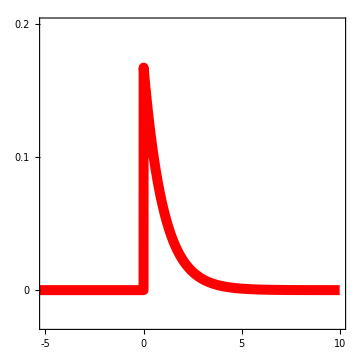

```mathematica
xmax=10;dx=0.0045;
t1=With[{A=Avalue,z=zvalue,ρ0=ρ0value},Table[{x,A/z Exp[-x]*HeavisideTheta[x]},{x,-xmax,xmax,dx}]];
p1=ListLinePlot[{t1},PlotStyle->{Directive[Red,Thickness-> 0.02],Directive[Red,Thick],Directive[Black,Thick]},PlotRange->{{-xmax/2,xmax},{-0.025,0.2}},FrameTicks->{{{0,0.1,0.2},None},{{-5,0,5,10},None}},Frame->True,FrameTicksStyle->Directive[Black,40,FontFamily->"CMU Serif"],AspectRatio->1,ImageSize->Medium]
```

```mathematica
dir=NotebookDirectory[];
opfile=StringJoin[dir,"del_rho_Lin_1D.txt"];
Export[opfile, t1,"Table"]
"/home/debsankar/Dropbox/Rituparno_Debsankar_Jyoti/active_droplets/fig_05/LT_flowprofilenew.png"
```

/home/debsankar/Desktop/jyoti_paper_gitupload/panel A/del_rho_Lin_1D.txt

/home/debsankar/Dropbox/Rituparno_Debsankar_Jyoti/active_droplets/fig_05/LT_flowprofilenew.png